## Define NV axes

```mathematica
(*define rodrigues rotation matrix for arbitary rotation of angle θ around an axis vec*)
Rrod[vec_,θ_]:= Module[{ux,uy,uz},{{ux,uy,uz} = {vec[[1]],vec[[2]],vec[[3]]};R = ({{Cos[θ]+ux^2(1-Cos[θ]), ux uy (1-Cos[θ])-uz Sin[θ], uz ux (1-Cos[θ]) + uy Sin[θ]}, {uy ux (1-Cos[θ])+uz Sin[θ], Cos[θ]+uy^2(1-Cos[θ]), uy uz (1-Cos[θ])-ux Sin[θ]}, {uz ux (1-Cos[θ]) - uy Sin[θ], uz uy (1-Cos[θ]) + ux Sin[θ], Cos[θ]+uz^2(1-Cos[θ])}})
}];

Rx[θ_] = Rrod[{1,0,0}, θ][[1]];(*rotation operator about x*)
Ry[θ_] = Rrod[{0,1,0}, θ][[1]];(*rotation operator about y*)
Rz[θ_] = Rrod[{0,0,1}, θ][[1]];(*rotation operator about z*)

(*100-NV unit vector*)
NVs100= 2/(√3){{1/2,1/2,1/2},{-1/2,-1/2,1/2},{1/2,-1/2,-1/2},{-1/2,1/2,-1/2}}; 
(*Rotate NVs to get 111 orientation*)
θm =1/2ArcCos[-1/3]; (*define angle for y rotn*)
NVs111 =FullSimplify[Table[(Ry[θm].(Rz[-π/4].NVs100[[i]]))/Norm[Ry[1/2θm].(Rz[π/4].NVs100[[i]])], {i,1,4}]] ;
(*Rotate NVs to get 110 orientation*)
NVs110 =Normalize/@FullSimplify[Table[Ry[-π/4].NVs100[[i]], {i,1,4}]] ;
```

## Define Projection operation for each NV axis and Spin matrices

```mathematica
(*make a coordinate system for the NV*)
MakeCS[nv_] := Module[{v1,v2,v3},
v1 = nv;
v2 = nv×{0,0,1};
v3 = (v1× v2)/(Norm[v1]Norm[v2]);
{v1,v2,v3}]
(*projects magnetic field along NV axjs ensuring Bz is along NV axis*)
Proj[B_, nv_]:= Module[{v1,v2,v3,vx,vy,vz,Bx,By,Bz},
{v1,v2,v3} = MakeCS[nv];
{vx,vy,vz} = {v2,v3,v1};
 {B.vx,B.vy,B.vz}]

Sx = 1/(√2)({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}});Sy = 1/√2({{0, -ⅈ, 0}, {ⅈ, 0, -ⅈ}, {0, ⅈ, 0}});Sz = ({{1, 0, 0}, {0, 0, 0}, {0, 0, -1}});
Stot = {Sx,Sy,Sz};
```

## Create Hyperfine Hamiltonian

```mathematica
(*now try including nuclear part of hamiltonian*)
Hzps=Dz*KroneckerProduct[Sz^2,IdentityMatrix[3]];   (*Electronic zero field splititng*)
Hqp=P*KroneckerProduct[IdentityMatrix[3],Sz^2];   (*Nuclear quadropole of N14*)
HzeemanE=γ*KroneckerProduct[Bx Sx+By Sy+Bz Sz,IdentityMatrix[3]];   (*electron zeeman splitting*)
HzeemanN=-γn*KroneckerProduct[IdentityMatrix[3], Bx Sx+By Sy+Bz Sz];   (*nuclear zeeman splitting*)
Hhf=A1*(KroneckerProduct[Sx, IdentityMatrix[3]].KroneckerProduct[IdentityMatrix[3],Sx]+KroneckerProduct[Sy, IdentityMatrix[3]].KroneckerProduct[IdentityMatrix[3],Sy])+Az*KroneckerProduct[Sz, IdentityMatrix[3]].KroneckerProduct[IdentityMatrix[3],Sz];  (*hyperfine interaction term between electronic and nuclear spins*)
MHz = 10^6;
(*define key parameters*)
numbers={Dz-> 2π*2870 MHz, P->-2π*4.9457MHz,γ-> 2π*2.803MHz,γn->2π*3.077*10^-4 MHz,A1->-2π*2.62MHz,Az->2π*2.2MHz};
(*A1->2π*2.14MHz,Az->2π*2.7MHz i dont think these are correct  current values from:Fast coherent control of nitrogen-14 spins associated with nitrogen-vacancy centers in diamonds using dynamical decoupling
P value from Robust optical readout and characterization of nuclear spin transitions
in nitrogen-vacancy ensembles in diamond*)

(*define full hamiltonian*)
HwithB[B_, nv_] =Module[{Bx, By, Bz,Hfull,HzeemanE,HzeemanN},
{Bx, By, Bz} = Proj[B,nv];
HzeemanE=γ*KroneckerProduct[Bx Sx+By Sy+Bz Sz,IdentityMatrix[3]];
HzeemanN=-γn*KroneckerProduct[IdentityMatrix[3], Bx Sx+By Sy+Bz Sz];
Hfull = Hzps+Hqp+HzeemanE+HzeemanN+Hhf];

(*Diagonalise hamiltonian based on B field and NV axis (vectors)*)
Energies[B_, nv_] :=Module[{Bx, By, Bz,Hfull,Ham, evals},
Ham= HwithB[B,nv]/.numbers;
evals =Sort[ 1/(2π MHz)Eigenvalues[Ham]];
evals]
lorentzian[x_, dx_, Γ_, amp_] = 1-(amp Γ^2)/((x-dx)^2+Γ^2);
```

```mathematica
GenSpec[B0_, θ_, ϕ_, w_, amp_]:=1/24 Total@Map[lorentzian[x, #,w,amp]&,Flatten@Map[{#[[2]]-#[[1]], #[[3]]-#[[1]]}&@Partition[Energies[{B0 Sin[θ] Cos[ϕ],B0 Sin[θ]Sin[ϕ],B0 Cos[θ]}, #],3]&, NVs100]]
```

### Generate an ODMR spectrum for B = 100G, θ = 25°, ϕ = 32°, with lorentzian widths = 2.25MHz and amplitude 0.1

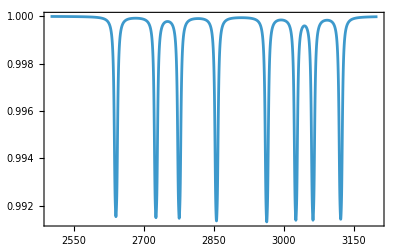

```mathematica
spec[x_]=GenSpec[100,25°, 32°, 2.25, 0.1];
Plot[spec[x], {x, 2500,3200}, PlotRange->All, Frame-> True]
```